# Practical 9

### Submitted By- Puranjyoti Bera (20201043)

Plot the segment ‘L’ joining the point A = 0 to B = 2 + i(ℼ/4) and give an exact calculation of ∫_L e^z ⅆz

The parameterization of L is given by

L:z(t)=(2+(ⅈ π)/4) t , 0⩽t⩽1

The plot of the segment L is given by the figure

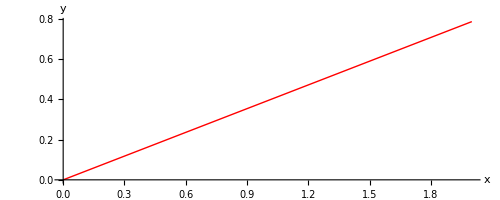

∫=-1+((1+ⅈ) ⅇ^2)/(√2)

```mathematica
w1:=0;
w2:=2+I*Pi/4;
z[t_]:=(1-t)*w1+t*w2;
Print["The parameterization of L is given by"];
Print["L:z(t)=",z[t]," , 0⩽t⩽1"];
Print["The plot of the segment L is given by the figure"]
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,1},PlotStyle-> {Thick,Red},AxesLabel->{x,y}]
f[z_]:=Exp[z];
Print["∫=", ComplexExpand[Integrate[f[z[t]]z'[t],{t,0,1}]]]
```